# Proofreading does not result in more reliable ligand discrimination in receptor signaling due to its inherent stochasticity

## Setup

```mathematica
expandParams={x->(c kon)/koff,g->koff/kf};
contractParams={c->koff/kon x,kf->koff/g};
cmap=ColorData[97,"ColorList"];
gradcolor={RGBColor[250/255,250/255,110/255],RGBColor[250/255,250/255,110/255],RGBColor[146/255,220/255,126/255],RGBColor[100/255,201/255,135/255],RGBColor[57/255,180/255,142/255],RGBColor[8/255,159/255,143/255],RGBColor[0/255,159/255,143/255],RGBColor[0/255,137/255,138/255],RGBColor[8/255,115/255,127/255],RGBColor[33/255,93/255,110/255],RGBColor[42/255,72/255,88/255]};

Pss0={koff/(koff+c kon),(c kon)/(koff+c kon)};
Pss1={koff/(koff+c kon),(c koff kon)/((kf+koff) (koff+c kon)),(c kf kon)/((kf+koff) (koff+c kon))};
Pss2={koff/(koff+c kon),(c koff kon)/((kf+koff) (koff+c kon)),(c kf koff kon)/((kf+koff)^2 (koff+c kon)),(c kf^2 kon)/((kf+koff)^2 (koff+c kon))};

μ0= kp t x/(1+x)/.expandParams;
μ1= (kp t)/(1+g)x/(1+x)/.expandParams;
μ2=(kp t)/(1+g)^2 x/(1+x)/.expandParams;
μ3=(kp t)/(1+g)^3 x/(1+x)/.expandParams;
μ4=(kp t)/(1+g)^4 x/(1+x)/.expandParams;
μN=(kp t)/(1+g)^Ns x/(1+x)/.expandParams;
```

```mathematica
(* All variances are given for large t *)
Σ0=(kp t x)/(1+x)+(2 kp^2 t x)/(koff(1+x)^3)/.expandParams;

Σ1=(kp t x ((1+g)^2 koff (1+x)^2+2 kp (1+g^2 (1+x)^2+g (2+x))))/((1+g)^3 koff (1+x)^3)/.expandParams;(*Limit of large t*)

Σ2=(kp t x ((1+g)^3 koff (1+x)^2+2 kp (1+3 g^2 (1+x)^2+g^3 (1+x)^2+g (3+2 x))))/((1+g)^5 koff (1+x)^3)/.expandParams;

Σ3=1/((1+g)^7 koff (1+x)^3)kp t x ((1+g)^4 koff (1+x)^2+2 kp (1+6 g^2 (1+x)^2+4 g^3 (1+x)^2+g^4 (1+x)^2+g (4+3 x)))/.expandParams;

Σ4=1/((1+g)^9 koff (1+x)^3)kp t x ((1+g)^5 koff (1+x)^2+2 kp (1+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5+4 x)))/.expandParams;
```

```mathematica
ΣN=(kp t x ((1+g)^(Ns+1) koff (1+x)^2+2 kp ((1+g)^(Ns+1) (1+x)^2-x (2+x+g (2+Ns+Ns x+x)))))/((1+g)^(1+2Ns) koff (1+x)^3);
(* (kp t x)/((1+x)(1+g)^Ns)+((2 kp^2 t x)/((koff+koff x)(1+g)^Ns)-(2 kp^2 t x^2 (2+x+g (2+Ns+Ns x+x)))/((1+g)^(1+2Ns) koff (1+x)^3)) *)
```

```mathematica
η0=(Pss0[[2]]/.koff->δ koff)/Pss0[[2]];
η1=(Pss1[[3]]/.koff->δ koff)/Pss1[[3]];
η2=(Pss2[[4]]/.koff->δ koff)/Pss2[[4]];
ηN=((kf+koff)^Ns (koff+c kon))/((kf+koff δ)^Ns (c kon+koff δ));
```

```mathematica
BPMetric[mean_,var_]:=(mean-(mean/.koff->δ koff))^2/(var+(var/.koff->δ koff))
```

```mathematica
κ0estimator=(koff/.Solve[μ0==n/.expandParams,koff][[1]]);
κ1estimator=(koff/.Solve[μ1==n/.expandParams,koff][[1]]);
κ2estimator=(koff/.Solve[μ2==n/.expandParams,koff][[2]]);
κ3estimator=(koff/.Solve[μ3==n/.expandParams,koff][[1]]);
κ4estimator=(koff/.Solve[μ4==n/.expandParams,koff][[1]]);

κ0=κ0estimator/.n->μ0;
κ1=κ1estimator/.n->μ1;
κ2=κ2estimator/.n->μ2;
κ3=κ3estimator/.n->μ3;
κ4=κ4estimator/.n->μ4;


Σk0=Σ0/D[Evaluate[μ0/.expandParams],koff]^2//Simplify;
Σk1=Σ1/D[Evaluate[μ1/.expandParams],koff]^2//Simplify;
Σk2=Σ2/D[Evaluate[μ2/.expandParams],koff]^2//Simplify;
Σk3=Σ3/D[Evaluate[μ3/.expandParams],koff]^2//Simplify;
Σk4=Σ4/D[Evaluate[μ4/.expandParams],koff]^2//Simplify;
Σk5=(ΣN/.Ns->5)/D[Evaluate[μN/.Ns->5/.expandParams],koff]^2//Simplify;
Σk6=(ΣN/.Ns->6)/D[Evaluate[μN/.Ns->6/.expandParams],koff]^2//Simplify;

ΣkN=Evaluate[ΣN/.expandParams]/D[μN,koff]^2//Simplify;
```

```mathematica
Σk1/.contractParams//FullSimplify
```

((1+g) koff (1+x) ((1+g)^2 koff (1+x)^2+2 kp (1+g (2+x+g (1+x)^2))))/(kp t x (1+g (2+x))^2)

```mathematica
((1+g) (1+x) (((1+g) koff (1+x))^2+2 kp koff ((1+g(1+x))^2-g x)))/(kp t x (1+g (2+x))^2)
```

((1+g) (1+x) ((1+g)^2 koff^2 (1+x)^2+2 koff kp (-g x+(1+g (1+x))^2)))/(kp t x (1+g (2+x))^2)

```mathematica
(*κ1 = (-1/kf(1+g x)+√((1+g x)^2+4g))/2*)
```

```mathematica
xgParams={kon->1,kp->1,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};
xgTicks={{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Table[{i,Superscript[10,i]},{i,-3,3}],None}};
gxTicks={{Table[{i,Superscript[10,i]},{i,-3,3}],None},{Table[{i,Superscript[10,i]},{i,-1,3}],None}};
```

```mathematica
SnR=μN/(√ΣN)/.expandParams;
SnRBP=κ1/(√Σk1);
KPR0BPn=BPMetric[μ0,Σ0];
KPR1BPn=BPMetric[μ1,Σ1];
KPR2BPn=BPMetric[μ2,Σ2];
KPR3BPn=BPMetric[μ3,Σ3];
KPR4BPn=BPMetric[μ4,Σ4];
KPR5BPn=BPMetric[Evaluate[μN/.Ns->5],Evaluate[ΣN/.Ns->5]];
KPRNBPn=BPMetric[μN,ΣN];

KPR0BPk=BPMetric[koff,Σk0];
KPR1BPk=BPMetric[koff,Σk1];
KPR2BPk=BPMetric[koff,Σk2];
KPR3BPk=BPMetric[koff,Σk3];
KPR4BPk=BPMetric[koff,Σk4];
KPR5BPk=BPMetric[koff,Σk5];
KPRNBPk=BPMetric[koff,ΣkN];
```

## Figures

#### 1B

```mathematica
m1=-0.5;
std1=0.5;
std2=1.25;
increment=2;
```

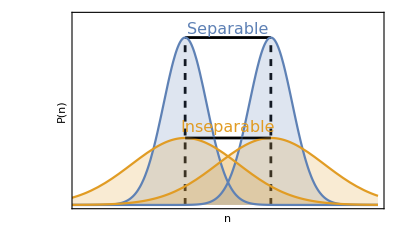

```mathematica
max1=Max[Table[PDF[NormalDistribution[m1,std1],x],{x,m1-0.1,m1+0.1,0.01}]];
max2=Max[Table[PDF[NormalDistribution[m1,std2],x],{x,m1-0.1,m1+0.1,0.01}]];
Fig1B=Show[
ListPlot[{Table[{m1,y},{y,0,1.05*max1,0.1}],Table[{m1+increment,y},{y,0,1.05*max1,0.1}],Table[{x,max1},{x,m1,m1+increment,0.1}],Table[{x,max2},{x,m1,m1+increment,0.1}]},

Joined->True,PlotStyle->{{Dashed,Black,Thickness[0.005]},{Dashed,Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},
Frame->{{True,False},{True,False}},FrameStyle->Black,LabelStyle->{Black,FontSize->24},FrameTicks->None,Axes->{True,False},PlotRange->{{-3,4},{0,0.9}},FrameLabel->{"n","P(n)"},

Epilog->{Line[{{m1,max1},{m1+increment,max1}}],Text[Style["Separable",cmap[[1]],FontSize->16],{m1+0.5*increment,1.05*max1}],
Line[{{m1,max2},{m1+increment,max2}}],Text[Style["Inseparable",cmap[[2]],FontSize->16],{m1+0.5*increment,1.15*max2}]
}],

Plot[{PDF[NormalDistribution[m1,std1],x],PDF[NormalDistribution[m1+increment,std1],x],PDF[NormalDistribution[m1,std2],x],PDF[NormalDistribution[m1+increment,std2],x]},{x,-4,4},
PlotStyle->{cmap[[1]],cmap[[1]],cmap[[2]],cmap[[2]]},
Filling->Axis]
]
```

#### 1C

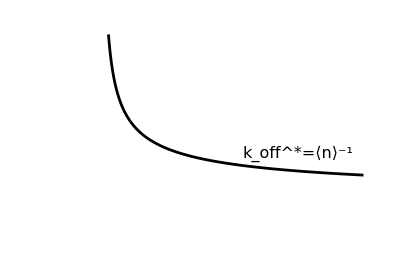
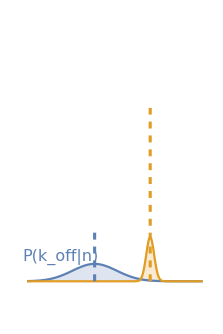
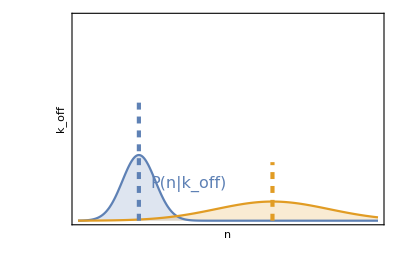

```mathematica
PnKofflabel=Style["P(n|k_off)",{FontSize->16,FontColor->cmap[[1]]}];
PKoffNlabel=Style["P(k_off|n)",{FontSize->16,FontColor->cmap[[1]]}];
MLElabel=Style["k_off^*=⟨n⟩^-1",16];
distParams={kon->1,kp->10,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};

d1Params={ctest->0,gtest->1};
n1dist={μ1/.distParams/.d1Params//N,Σ1/.distParams/.d1Params//N};
κ1estimator/.{n->n1dist[[1]]}/.distParams/.d1Params;
Σk1/.{n->n1dist[[1]]}/.distParams/.{ctest->0,gtest->Log10[%]};
k1dist={%%,%};

d2Params={ctest->0,gtest->0.55};
n2dist={μ1/.distParams/.d2Params//N,Σ1/.distParams/.d2Params//N};
κ1estimator/.{n->n2dist[[1]]}/.distParams/.d2Params;
Σk1/.{n->n2dist[[1]]}/.distParams/.{ctest->1,gtest->Log10[%]};
k2dist={%%,%};

g1=
Show[
Plot[{PDF[NormalDistribution[n1dist[[1]],√n1dist[[2]]],x],PDF[NormalDistribution[n2dist[[1]],√n2dist[[2]]],x]},
{x,-10,80},
Frame->{{True,False},{True,False}},FrameLabel->{"n","k_off"},FrameStyle->{{{Black,Thickness[0.005]},None},{{Black,Thickness[0.005]},None}},LabelStyle->{Black,FontSize->16},FrameTicks->None,Axes->{False,False},PlotStyle->{cmap[[1]],cmap[[2]]},Filling->Axis,PlotRange->{{-10,80},{0,0.25}},AspectRatio->2/3,Epilog->Inset[PnKofflabel,{23,0.045}]],

ListPlot[Table[{n1dist[[1]],i},{i,0,0.15,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[1]],Dashed,Thickness[0.0075]},PlotRange->{{-10,50},{0,0.25}},AspectRatio->2/3],

ListPlot[Table[{n2dist[[1]],i},{i,0,0.072,0.001}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[2]],Dashed,Thickness[0.0075]},PlotRange->{{-10,50},{0,0.25}},AspectRatio->2/3]
];

g2=Plot[κ1estimator/.xgParams/.ctest->0,{n,2,80},
PlotRange->{{-20,80},{-2.7,6.5}},PlotStyle->{Black,Thickness[0.005]},Frame->False,Axes->False,AspectRatio->2/3,
Epilog->Inset[MLElabel,{60,1},Automatic,Automatic]];

g3=Rotate[
Show[

Plot[{PDF[NormalDistribution[k1dist[[1]],√k1dist[[2]]],-k],0.45*PDF[NormalDistribution[-1.78+k2dist[[1]],√k2dist[[2]]],-k]},
{k,-20,6},PlotStyle->{cmap[[1]],cmap[[2]]},
PlotRange->{{-21,6},{-0.155,1.75}},Filling->Axis,Frame->{{False,False},{False,False}},
FrameStyle->Black,LabelStyle->{Black,FontSize->16},FrameTicks->None,Axes->{False,False},AspectRatio->3/2,ImageSize->223,Epilog->Inset[PKoffNlabel,{-15,0.17}]],
ListPlot[Table[{-k1dist[[1]],i},{i,0,0.37,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[1]],Dashed,Thickness[0.01]},PlotRange->{{-6.5,1},{-0.23,1.75}}],
ListPlot[Table[{1.78-k2dist[[1]],i},{i,0,1.21,0.01}],Axes->{False,False},Frame->False,Joined->True,PlotStyle->{cmap[[2]],Dashed,Thickness[0.01]},PlotRange->{{-6.5,1},{-0.23,1.75}}]

],-π/2];
Fig1C=Overlay[{g2,g3,g1}]
```

#### 2A

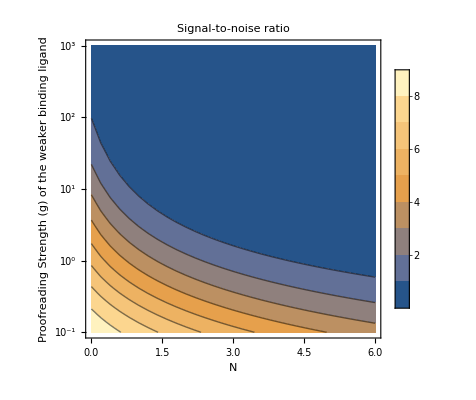

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,c->10^ctest,kf->1};
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Signal-to-noise ratio",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
data=Flatten[Table[{NTEST,GTEST,μN/√ΣN}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
Fig2A=ListContourPlot[data,Evaluate@plotOptions]
```

#### 2B

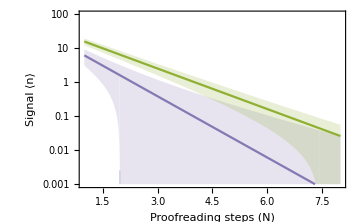

```mathematica
grep=g->3;
δrep={δ->0.5};
suppParams=Join[{kon->1,kp->1,t->100,koff->g,c->1,kf->1},δrep]/.grep;
curves1={μN,μN+√ΣN,Max[μN-√ΣN,10^-8]}/.expandParams/.suppParams;
curves2={μN,μN+√ΣN,Max[μN-√ΣN,10^-8]}/.{koff->δ koff}/.expandParams/.suppParams;
plotOptions={Filling->{1->{2},1->{3}},
LabelStyle->{Black,FontSize->18},
TicksStyle->Black,
ImageSize->Medium,
Frame->{{True,False},{True,False}},
Filling->{1->{2},1->{3},4->{5},6->{4}},
FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-9,4,1}],None},{Automatic,None}},
PlotRange->{{1,8},{10^-3,10^2}},
FrameLabel->{"Proofreading steps (N)","Signal ⟨n⟩"}};

g1=LogPlot[curves1,{Ns,1,8},PlotStyle->{cmap[[5]],None,None},Evaluate@plotOptions];
g2=LogPlot[curves2,{Ns,1,8},PlotStyle->{cmap[[3]],None,None},Evaluate@plotOptions];
Fig2B=Show[g1,g2]
```

#### 2C

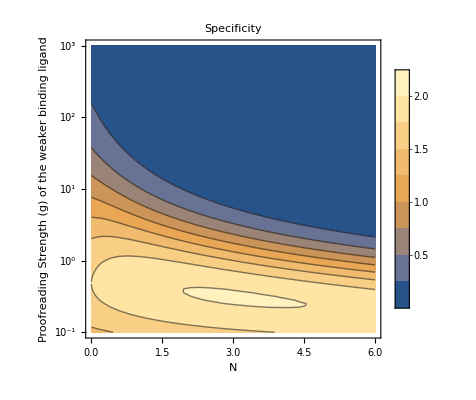

```mathematica
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Specificity",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
data=Flatten[Table[{NTEST,GTEST,koff/√ΣkN}/.xgParams/.{ctest->-1,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
Fig2C=ListContourPlot[data,Evaluate@plotOptions]
```

#### 3A

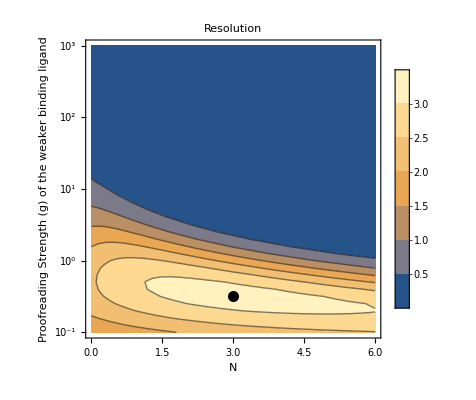

```mathematica
data=Flatten[Table[{NTEST,GTEST,BPMetric[koff,ΣkN]}/.xgParams/.{ctest->-1,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.1},{NTEST,0,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Resolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
Fig3A=ListContourPlot[data,Evaluate@plotOptions,
Epilog->{PointSize[0.02],{Black,Point[{EpilogPoint[[1]],EpilogPoint[[2]]}]}}]
```

#### 3B

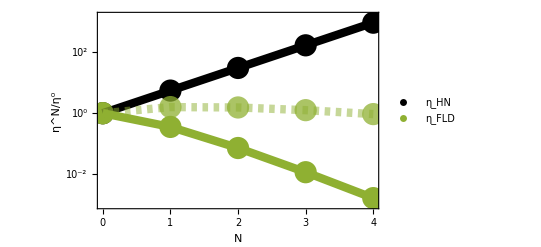

```mathematica
testpoint={ctest->0,gtest->1};
testpoint2={ctest->0,gtest->0};
yticks=Table[{2.301i,Superscript[10,i]},{i,-4,4}];
p1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,4,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.04],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.001,1500}}];
p2=LogPlot[ηN/η0/.xgParams/.testpoint,{Ns,0,4},PlotStyle->{Thickness[0.015],Black}];



BPKscale={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.expandParams/.xgParams/.testpoint;
BPKscale2={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.expandParams/.xgParams/.testpoint2;
Fig3B=Legended[
Show[p1,p2,

ListLogPlot[BPKscale,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[BPKscale,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],

ListLogPlot[BPKscale2,PlotStyle->{cmap[[3]],PointSize[0.04],Opacity[0.75]}],
ListLogPlot[BPKscale2,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015],Dashing[0.01],Opacity[0.5]}]
],
PointLegend[{Black,cmap[[3]]},{"η_HN","η_FLD"},LegendMarkerSize->25]]
```

#### 4A

```mathematica
MeanM0=β(koff t x)/(1+x);
VarM0=β^2(koff t x (1+x^2))/(1+x)^3;(*(x (-2 ⅇ^(-koff t (1+x)) x+koff t (1+x) (1+x^2)))/(1+x)^4;*)
MeanM1=β(koff t x)/((1+x)(1+g));
VarM1=β^2(koff t x (1+2 g+x^2+g^2 (1+x)^2))/((1+g)^3 (1+x)^3);
MeanM2=β(koff t x)/((1+g)^2 (1+x));
VarM2=β^2(koff t x ((1+g)^3+2 g^2 (3+g) x+(1+g (-1+g (3+g))) x^2))/((1+g)^5 (1+x)^3);
MeanM3=β(koff t x)/((1+g)^3 (1+x));
VarM3=β^2(koff t x ((1+g)^4+2 g^2 (6+g (4+g)) x+(1+g (-2+g (6+g (4+g)))) x^2))/((1+g)^7 (1+x)^3);
MeanM4=β(koff t x)/((1+g)^4 (1+x));
VarM4=β^2(koff t x (1+x^2+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5-3 x^2)))/((1+g)^9 (1+x)^3);
MeanM5=(koff t x)/((1+g)^5 (1+x));


Σk0G=(VarM0/.expandParams)/D[Evaluate[MeanM0/.expandParams],koff]^2//Simplify;
Σk1G=(VarM1/.expandParams)/D[Evaluate[MeanM1/.expandParams],koff]^2//Simplify;
Σk2G=(VarM2/.expandParams)/D[Evaluate[MeanM2/.expandParams],koff]^2//Simplify;
Σk3G=(VarM3/.expandParams)/D[Evaluate[MeanM3/.expandParams],koff]^2//Simplify;
Σk4G=(VarM4/.expandParams)/D[Evaluate[MeanM4/.expandParams],koff]^2//Simplify;


KPRG0FLD=BPMetric[koff,Σk0G];
KPRG1FLD=BPMetric[koff,Σk1G];
KPRG2FLD=BPMetric[koff,Σk2G];
KPRG3FLD=BPMetric[koff,Σk3G];
KPRG4FLD=BPMetric[koff,Σk4G];

KPRG0HN=(MeanM0/.expandParams/.koff->δ koff)/(MeanM0/.expandParams);
KPRG1HN=(MeanM1/.expandParams/.koff->δ koff)/(MeanM1/.expandParams);
KPRG2HN=(MeanM2/.expandParams/.koff->δ koff)/(MeanM2/.expandParams);
KPRG3HN=(MeanM3/.expandParams/.koff->δ koff)/(MeanM3/.expandParams);
KPRG4HN=(MeanM4/.expandParams/.koff->δ koff)/(MeanM4/.expandParams);
KPRGNHN=(((koff t x)/((1+g)^Ns (1+x)))/.expandParams/.koff->δ koff)/(((koff t x)/((1+g)^Ns (1+x)))/.expandParams);
```

Note that the variance in the G-protein signal has an asymptote for each model N with N>0. Avoid choosing conditions that match the asymptote for both koff and δ×koff.

```mathematica
xgParams
```

{kon→1,kp→1,t→100,koff→10^gtest,δ→0.1,c→10^ctest,kf→1}

```mathematica
testpoint={ctest->1,gtest->0,β->1};
testpoint2={ctest->1,gtest->Log10[3],β->1};


AnyTrue[Table[Abs[ΣkGundefined/.Ns->i/.xgParams/.testpoint],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.Ns->i/.xgParams/.testpoint2],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.{Ns->i,koff->δ koff}/.xgParams/.testpoint],{i,1,4}],#<0.01&]
AnyTrue[Table[Abs[ΣkGundefined/.{Ns->i,koff->δ koff}/.xgParams/.testpoint2],{i,1,4}],#<0.01&]
```

Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01

Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01

Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01||Abs[ΣkGundefined]<0.01

«1 more identical outputs»

```mathematica
Table[ΣkGundefined/.{koff->10,kf->1,c->1,kon->1,δ->0.1},{Ns,0,6}]
Table[ΣkGundefined/.{koff->5,kf->1,c->1,kon->1,δ->0.1},{Ns,0,6}]
```

{ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined}

{ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined,ΣkGundefined}

```mathematica
KPRG0FLD/.contractParams//Simplify
KPRG1FLD/.contractParams//Simplify
KPRG2FLD/.contractParams//Simplify
```

(koff t x^3 (-1+δ)^2)/(1+δ^4+x^3 (1+δ)+x^2 (1+δ^2)+x (1+δ^3))

(t x (koff-koff δ)^2)/(koff (((1+g) (1+x) (1+2 g+x^2+g^2 (1+x)^2))/(g-x)^2+(δ (x+δ) (1+g δ) (2 g^2 x δ^3+δ^2 (1+g δ)^2+x^2 (1+g^2 δ^2)))/((x-g δ^2)^2)))

(t x (koff-koff δ)^2)/(koff (((1+g) (1+x) (1+x^2+3 g^2 (1+x)^2+g^3 (1+x)^2-g (-3+x^2)))/(x-g (2+x))^2+(δ (x+δ) (1+g δ) (δ^2 (1+g δ)^3+2 g^2 x δ^3 (3+g δ)+x^2 (1-g δ+3 g^2 δ^2+g^3 δ^3)))/((2 g δ^2+x (-1+g δ))^2)))

```mathematica
HNReviwer2ModelSimMedC={{0,1.00},{1,3.30},{2,17.04},{3,87.55},{4,796.22}};

FLDReviewer2ModelSimHighC={{0,1.00},{1,82.52},{2,326.91},{3,204.24},{4,94.01}};
FLDReviewer2ModelSimMedC={{0,1.00},{1,706.11},{2,798.36},{3,371.34},{4,149.72}};
FLDReviewer2ModelSimLowC={{0,1.00},{1,733.09},{2,523.14},{3,318.13},{4,135.05}};

FLDReviewer2ModelSimτIs1OverKOFF={{0,1.0000},{1,2.1582},{2,4.4224},{3,4.1726},{4,3.9602},{5,2.7774}};
FLDReviewer2ModelSimτIs1OverKOFHighG={{0,1.0000},{1,2.6509},{2,2.2813},{3,1.3466},{4,0.6453},{5,0.2547}};
FLDReviewer2ModelSimτIs1OverKOFFLowC={{0,1.0000},{1,1073.7280},{2,758.3255},{3,316.6415},{4,269.3606},{5,107.7563}};
FLDReviewer2ModelSimτIs1OverKOFFHighC={{0,1.0000},{1,0.0071},{2,0.0606},{3,0.0340},{4,0.0137},{5,0.0065}};

AllDetFLD={{0,1.0000},{1,1.5281},{2,4.3959},{3,4.9465},{4,3.7004}};
AllDetFLDHighG={{0,1.0000},{1,2.4888},{2,1.5772},{3,1.0520},{4,0.4475}};
AllDetHN={{0,1.00},{1,3.03},{2,8.51},{3,24.21},{4,94.45}};
```

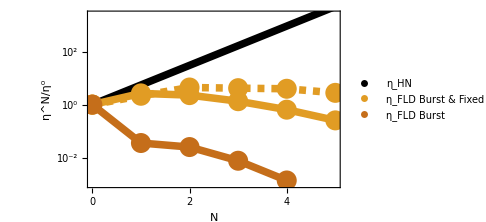

```mathematica
SNRn=μN/ΣN/.contractParams;
SNR0=μ0/Σ0/.contractParams;

testpoint={ctest->1,gtest->1,β->10};
testpoint2={ctest->1,gtest->1,kf->10/3,β->10};
yticks=Table[{2.301i,Superscript[10,i]},{i,-4,4}];
p1=ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,5,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4,5},None}},PlotRange->{Automatic,{0.001,2500}}];
p2=LogPlot[KPRGNHN/KPRG0HN/.xgParams/.testpoint,{Ns,0,5},PlotStyle->{Thickness[0.015],Black}];


BPKscale={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint;
BPKscale2={{0,1},{1,KPR1BPk/KPR0BPk},{2,KPR2BPk/KPR0BPk},{3,KPR3BPk/KPR0BPk},{4,KPR4BPk/KPR0BPk}}/.xgParams/.testpoint;
FLDReviewer2ModelSim={{0,1.00},{1,1044.30},{2,553.45},{3,215.77},{4,92.01}};
FLDReviewer2ModelSimHighG={{0,1.00},{1,652.46},{2,84.63},{3,6.89},{4,0.64}};

KPRGFLD1={{0,1},{1,KPRG1FLD/KPRG0FLD},{2,KPRG2FLD/KPRG0FLD},{3,KPRG3FLD/KPRG0FLD},{4,KPRG4FLD/KPRG0FLD}}/.xgParams/.testpoint;

Fig4A=Legended[
Show[p1,p2,

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015],Dashed}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFHighG,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFHighG,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015]}],

ListLogPlot[KPRGFLD1,PlotStyle->{cmap[[6]],PointSize[0.04]}],
ListLogPlot[KPRGFLD1,Joined->True,PlotStyle->{cmap[[6]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,cmap[[2]],cmap[[6]]},{"η_HN","η_FLD\nBurst &\nFixed residence time","η_FLD\nBurst"},LegendMarkerSize->25]]
```

#### 4B

```mathematica
FLDReviewer2ModelSimLongTime500={{0,1.00},{1,22989.68},{2,16091.00},{3,6577.72},{4,2813.05}};

FLDReviewer2ModelSimShortTime50={{0,1.00},{1,0.97},{2,0.56},{3,0.26},{4,0.12}};
(*{{0,1.00},{1,1455.89},{2,1479.28},{3,656.58},{4,300.28}};*)(*G protein, β=1*)
(*{{0,1.00},{1,2640.67},{2,2825.06},{3,1428.18},{4,619.68}};*)(*Burst size 10*)

FLDReviewer2ModelSimShortTime5={{0,1.00},{1,0.99},{2,0.58},{3,0.24},{4,0.09}};
(*{{0,1.00},{1,8.59},{2,5.33},{3,2.09},{4,0.79}};*)(*G protein, β=1*)
(*{{0,1.00},{1,161.42},{2,88.62},{3,47.10},{4,16.64}};*)(*Burst size 10*)

FLDReviewer2ModelSimShortTime05={{0,1.00},{1,0.92},{2,0.32},{3,0.05},{4,0.02}};
(*{{0,1.00},{1,189.44},{2,70.33},{3,21.23},{4,3.25}};*)(*G protein, β=1*)
(*{{0,1.00},{1,135.41},{2,59.19},{3,25.22},{4,3.58}}*)(*Burst size 10*)
combined={FLDReviewer2ModelSimShortTime05,FLDReviewer2ModelSimShortTime5,FLDReviewer2ModelSimShortTime50};

FLDtheory={{0,1},{1,KPR1BPn/KPR0BPn},{2,KPR2BPn/KPR0BPn},{3,KPR3BPn/KPR0BPn},{4,KPR4BPn/KPR0BPn}}/.xgParams/.{ctest->1,gtest->1};
```

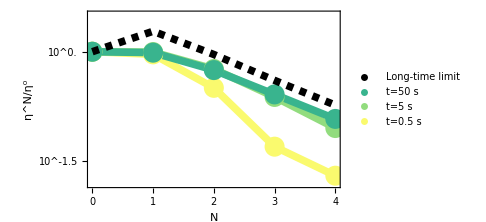

```mathematica
Fig4B=Show[
Legended[ListLogPlot[combined,
Joined->True,
PlotStyle->Table[{Thickness[0.015],gradcolor[[i]]},{i,1,7,2}],
Frame->{{True,False},{True,False}},

FrameLabel->{"N","η^N/η^0"},
FrameStyle->Black,
FrameTicksStyle->{Black,FontSize->16},
LabelStyle->{Black,FontSize->16},

FrameTicks->{{Table[{2.3i,Superscript[10,i]},{i,-3,4,0.5}],None},{{0,1,2,3,4},None}},
PlotRange->{Automatic,{Automatic,10^0.51}},
ImageSize->Medium],
PointLegend[Join[{Black},Table[gradcolor[[i]],{i,5,1,-2}]],{"Long-time limit","t=50 s","t=5 s","t=0.5 s"},LegendMarkerSize->25]],
ListLogPlot[combined,PlotStyle->Table[{PointSize[0.04],gradcolor[[i]]},{i,1,7,2}]],
ListLogPlot[FLDtheory,Joined->True,PlotStyle->{Black,Thickness[0.015],Dashed}]
]
```

#### 4C

```mathematica
(*μ/.c->ω c/.params*)
```

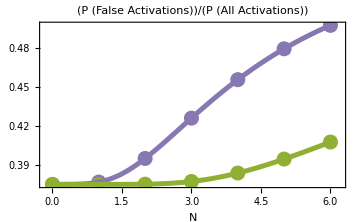

```mathematica
testparams={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.1};
testparams2={kon->1,kp->1,t->100,koff->1,δ->0.1,c->1,kf->0.3};
FPoAp[μ_,σ_,params_,ω_:10]:=Module[{th=InverseCDF[NormalDistribution[μ/.c->ω c/.params,σ/.c->ω c/.params],0.40]},
((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])/((1-CDF[NormalDistribution[μ/.c->ω c,σ/.c->ω c],th])+(1-CDF[NormalDistribution[μ/.koff->δ koff,σ/.koff->δ koff],th]))/.params)
]
Fig4C=Show[
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6}]
},
Joined->False,
PlotRange->{{-0.15,6.2},Automatic},
PlotLabel->"(P (False Activations))/(P (All Activations))",
Frame->{{True,False},{True,False}},
FrameLabel->{"N",None},
FrameStyle->Black,
LabelStyle->{Black,FontSize->16},
PlotStyle->{{cmap[[5]],PointSize[0.03]},{cmap[[3]],PointSize[0.03]}},
ImageSize->Medium],
ListPlot[
{Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams,1]},{Ns,0,6,0.05}],
Table[{Ns,FPoAp[μN/.expandParams,√ΣN/.expandParams,testparams2,1]},{Ns,0,6,0.05}]
},

Joined->True,
PlotStyle->{{cmap[[5]],Thickness[0.01]},{cmap[[3]],Thickness[0.01]}},
ImageSize->Medium]
]
```

## Supplementary Figures

#### Derivations for G-protein KPR mean and variance

```mathematica
M0={{-kon c,koff},{kon c , -koff}};
M1={{-kon c,koff,koff},{kon c,-koff-kf,0},{0,kf,-koff}};
M2={{-kon c,koff,koff,koff},{kon c,-koff-kf,0,0},{0,kf,-koff-kf,0},{0,0,kf,-koff}};
M3={{-kon c,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0},{0,kf,-koff-kf,0,0},{0,0,kf,-koff-kf,0},{0,0,0,kf,-koff}};
M4={{-kon c,koff,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0,0},{0,kf,-koff-kf,0,0,0},{0,0,kf,-koff-kf,0,0},{0,0,0,kf,-koff-kf,0},{0,0,0,0,kf,-koff}};
M5={{-kon c,koff,koff,koff,koff,koff,koff},{kon c,-koff-kf,0,0,0,0,0},{0,kf,-koff-kf,0,0,0,0},{0,0,kf,-koff-kf,0,0,0},{0,0,0,kf,-koff-kf,0,0},{0,0,0,0,kf,-koff-kf,0},{0,0,0,0,0,kf,-koff}};
```

```mathematica
Pss0={P0,P1}/.(Solve[Join[Table[(M0.{P0,P1})[[i]]==0,{i,1,1}],{P0+P1==1}],{P0,P1}][[1]]);
Pss1={P0,P1,P2}/.(Solve[Join[Table[(M1.{P0,P1,P2})[[i]]==0,{i,1,2}],{P0+P1+P2==1}],{P0,P1,P2}][[1]]);
Pss2={P0,P1,P2,P3}/.(Solve[Join[Table[(M2.{P0,P1,P2,P3})[[i]]==0,{i,1,3}],{P0+P1+P2+P3==1}],{P0,P1,P2,P3}][[1]]);
Pss3={P0,P1,P2,P3,P4}/.(Solve[Join[Table[(M3.{P0,P1,P2,P3,P4})[[i]]==0,{i,1,4}],{P0+P1+P2+P3+P4==1}],{P0,P1,P2,P3,P4}][[1]]);
Pss4={P0,P1,P2,P3,P4,P5}/.(Solve[Join[Table[(M4.{P0,P1,P2,P3,P4,P5})[[i]]==0,{i,1,5}],{P0+P1+P2+P3+P4+P5==1}],{P0,P1,P2,P3,P4,P5}][[1]]);
Pss5={P0,P1,P2,P3,P4,P5,P6}/.(Solve[Join[Table[(M5.{P0,P1,P2,P3,P4,P5,P6})[[i]]==0,{i,1,6}],{P0+P1+P2+P3+P4+P5+P6==1}],{P0,P1,P2,P3,P4,P5,P6}][[1]]);
```

```mathematica
mMean[M_,Pss_]:=Module[{ndims=Length[Pss]},M[[ndims,ndims-1]] t Pss[[ndims-1]]]

mVariance[M_,Pss_]:=Module[{ndims,npartials,nEqs,nfVec,nSol,nSubMeans,dNSQUAREdt,NSQUARE,meanM,CovNN},
ndims=Length[M];
npartials=Table[Symbol["n"<>ToString[i]],{i,1,ndims}];
nfVec=Table[0,{i,1,ndims}];
nfVec[[ndims]]=M[[ndims,ndims-1]] Pss[[ndims-1]];

nEqs=Join[
Table[D[npartials[[i]][t],t]==M[[i]].Table[npartials[[i]][t],{i,1,ndims}]+nfVec[[i]],{i,1,ndims}],
Table[npartials[[i]][0]==0,{i,1,ndims}]];
nSol=DSolve[nEqs,npartials,t];
nSubMeans=Table[Evaluate[npartials/.nSol[[1]]][[i,2]],{i,1,ndims}];

dNSQUAREdt=2M[[ndims,ndims-1]] nSubMeans[[ndims-1]]+M[[ndims,ndims-1]] Pss[[ndims-1]];
NSQUARE=Integrate[dNSQUAREdt,t] // Simplify ;
meanM=M[[ndims,ndims-1]] t Pss[[ndims-1]];
CovNN=NSQUARE- meanM^2//Simplify;
CovNN
]
contractParams={c->(koff x)/kon,kf->koff/g};
expandParams={x->(kon c)/koff,g->koff/kf};
noExp={ⅇ^(-koff t (1+x))->0,ⅇ^(-(koff t (1+g+g x))/g)->0,ⅇ^(-(koff t (1+g (2+x)))/g)->0,ⅇ^(-((1+g) koff t)/g)->0,ⅇ^(-t (2 koff+koff/g+koff x))->0};
```

```mathematica
(* Confirmed from PRE paper *)
mMean[M0,Pss0]/.contractParams//Simplify
(mVariance[M0,Pss0]/.contractParams//FullSimplify)/.noExp
```

(koff t x)/(1+x)

(koff t x (1+x^2))/(1+x)^3

```mathematica
mMean[M1,Pss1]/.contractParams//Simplify
(mVariance[M1,Pss1]/.contractParams//FullSimplify)/.noExp
```

(koff t x)/(1+g+x+g x)

(koff t x (1+2 g+x^2+g^2 (1+x)^2))/((1+g)^3 (1+x)^3)

```mathematica
mMean[M2,Pss2]/.contractParams//Simplify
(mVariance[M2,Pss2]/.contractParams//FullSimplify)/.noExp//FullSimplify
```

(koff t x)/((1+g)^2 (1+x))

(koff t x ((1+g)^3+2 g^2 (3+g) x+(1+g (-1+g (3+g))) x^2))/((1+g)^5 (1+x)^3)

```mathematica
mMean[M3,Pss3]/.contractParams//Simplify
(mVariance[M3,Pss3]/.contractParams//FullSimplify)/.noExp//FullSimplify
```

(koff t x)/((1+g)^3 (1+x))

(koff t x ((1+g)^4+2 g^2 (6+g (4+g)) x+(1+g (-2+g (6+g (4+g)))) x^2))/((1+g)^7 (1+x)^3)

```mathematica
mMean[M4,Pss4]/.contractParams//Simplify
(mVariance[M4,Pss4]/.contractParams)/.noExp//Simplify
```

(koff t x)/((1+g)^4 (1+x))

(koff t x (1+x^2+10 g^2 (1+x)^2+10 g^3 (1+x)^2+5 g^4 (1+x)^2+g^5 (1+x)^2+g (5-3 x^2)))/((1+g)^9 (1+x)^3)

```mathematica
mMean[M5,Pss5]/.contractParams//Simplify
(mVariance[M5,Pss5]/.contractParams)/.noExp//Simplify
```

(koff t x)/((1+g)^5 (1+x))

#### S1A

Entropy: H[x]= - Integrate[P(x) Log[P(x)], dx]
Conditional entropy: H[x|y]= - Integrate[P(y) Integrate[P(x|y) Log[P(x|y)], dx], dy]


Prior on koff will be log-normal centered at koff=1.
Prior on n will be exponential ~ λ e^(-λ n) where λ=(kp*t)^-1
MI = H(koff) - H(koff|n)
and H(koff)= - Integrate[P[koff] Log[P[koff]],{koff,0,1000}]
and H(koff|n)= - Integrate[P[koff,n] Log[P[koff,n]/P[n]],{n,0,1000}, {koff,0,1000}]
Define: P[koff,n]=P[n|koff]P[koff]

```mathematica
Pkoff[koff_,μ_:0,σ_:1]:=1/(σ koff √(2π))E^(-1/2((Log[koff]-μ)/σ)^2);(*Log-normal PDF*)
(*Pkoff[koff_]:=10 E^(-10koff);Exponential PDF*)
```

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=1,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];
MIlist={};
MethodList={"GlobalAdaptive","LocalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive"};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->MethodList[[i+1]]];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity}];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=10,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];
MIlist={};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{n,0,Infinity},{k,0,Infinity}];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity}];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

```mathematica
Pnlk[n_,koff_,Ns_]:=Module[{c=1,kf=0.1,kon=1,kp=1,t=100,σn,μ},
μ=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff));
σn=σn=(c (1+koff/kf)^-Ns kon kp t)/(koff (1+(c kon)/koff))+(2 c (1+koff/kf)^-Ns kon kp^2 t)/(koff (koff+c kon))-(2 c^2 (1+koff/kf)^(-1-2 Ns) kon^2 kp^2 (2+(c kon)/koff+(koff (2+(c kon)/koff+Ns+(c kon Ns)/koff))/kf) t)/(koff^3 (1+(c kon)/koff)^3);
1/(√(2π σn))E^(-1/2((n-μ)/(√σn))^2)];

MIlist={};
MethodList={"GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","GlobalAdaptive","LocalAdaptive","MultiPeriodic","MultiPeriodic","MultiPeriodic"};
For[i=0,i<8,i++,
Print[i];
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->MethodList[[i+1]]];
Print[HNK];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity},Method->MethodList[[i+1]]];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity},Method->"DoubleExponential"];
AppendTo[MIlist,HN-HNK];
]
MIlist
```

```mathematica
MIfunc[i_]:=Module[{},
HNK=-NIntegrate[Pkoff[k,1,2]Pnlk[n,k,i] Log2[Pnlk[n,k,i]],{k,0,Infinity},{n,0,Infinity},Method->"LocalAdaptive"];
Pn[n_]:=NIntegrate[Pnlk[n,k,i]Pkoff[k,1,2],{k,0,Infinity}];
HN=-NIntegrate[Pn[n]Log2[Pn[n]],{n,0,Infinity},Method->"Trapezoidal"];
HN-HNK];
Table[MIfunc[i],{i,3.7,5,0.25}]
```

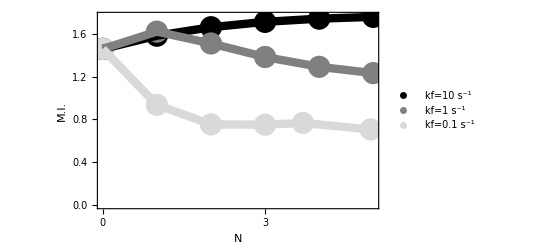

```mathematica
MIkf1={1.4586234168542846,1.6201963259109666,1.509360426851682,1.3831463627072238,1.291142465738909,1.2321310106120862,1.197423060641263,1.1795770826689};
MIkf10={1.458623416854282,1.5820537157474002,1.661444709778209,1.711523290947282,1.7416816409602305,1.7580998315221796,1.764945337975520,1.7651000926};

MIkf01={1.4586234168542838,0.9358591486210588,0.7528604190317278,0.7504920122990175,0.7663777316778799,0.7055385551710409};
(*{1.4586,0.93586,0.75286,0.75049,0.8038,0.8746,0.9491,1.020,1.0758,1.0948,1.200}; default integration method*)
MIkf1μ1σ2={2.1010413170152393,1.939991649078964,1.7801920904050719,1.7413582617142778,1.7173647306907396,1.7146611882781342,1.7237600820756558,1.7396216436820804};
MIkf10μ1σ2={2.101041317015243,2.136944802366786,2.1390110962123603,2.137734840665605,2.1044832915135023,2.09617625708177,2.088611079849956,2.1351653048528654};
MIkf01μ1σ2={{0,2.1010413157474845},{1,1.3320161093891159},{2,1.1920175744839234},{3,1.2247099091025684}};


comb1=Table[{j-1,MIkf1[[j]]},{j,1,Length[MIkf1]}];
comb2=Table[{j-1,MIkf10[[j]]},{j,1,Length[MIkf10]}];
comb3=Table[{j-1,MIkf01[[j]]},{j,1,Length[MIkf01]}];
comb3[[6,1]]=4.95;
comb3[[5,1]]=3.7;
comb4=Table[{j-1,MIkf1μ1σ2[[j]]},{j,1,Length[MIkf1μ1σ2]}];
comb5=Table[{j-1,MIkf10μ1σ2[[j]]},{j,1,Length[MIkf10μ1σ2]-1}];
comb6=MIkf01μ1σ2;

FigS1A=Legended[
Show[
ListPlot[{comb2,comb1,comb3},
Frame->{{True,False},{True,False}},FrameLabel->{"N","M.I."},LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{{PointSize[0.04],Black},{PointSize[0.04],Gray},{PointSize[0.04],LightGray}},FrameTicks->{{Automatic,None},{{0,1,2,3,4,5,6,7,8,9,10},None}},PlotRange->{{0,5},Automatic}],
ListPlot[{comb2,comb1,comb3},Joined->True,PlotStyle->{{Black,Thickness[0.015]},{Gray,Thickness[0.015]},{LightGray,Thickness[0.015]}}]
],
PointLegend[{Black,Gray,LightGray},{"kf=10 s^-1","kf=1 s^-1","kf=0.1 s^-1"},LegendMarkerSize->25]
]
```

#### S1B

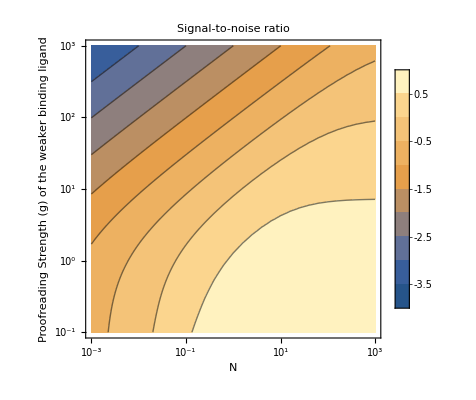

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,c->10^ctest,kf->1};
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
PlotLabel->"Signal-to-noise ratio",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Table[{i,Superscript[10,i]},{i,-3,3}],None}}};
data=Flatten[Table[{CTEST,GTEST,Log10[μ1/√Σ1]}/.expandParams/.estimateParams/.{ctest->CTEST,gtest->GTEST},{GTEST,-1,3,0.05},{CTEST,-3,3,0.2}],1];
FigS1B=ListContourPlot[data,Evaluate@plotOptions]
```

#### S1C

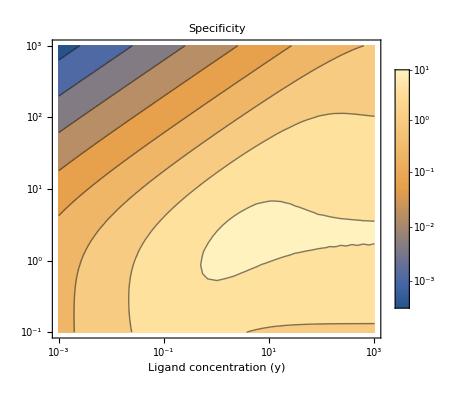

```mathematica
FigS1DtickSFs={1.068,1.065,1.04,1.5,1};
FigS1Dticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-3,1,1}];
FigS1Dticks=Table[{FigS1DtickSFs[[i]]*FigS1Dticks[[i,1]],FigS1Dticks[[i,2]]},{i,1,Length[FigS1Dticks]}];
FigS1DbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Dticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},8,LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1C=ContourPlot[Log10[SnRBP]/.expandParams/.xgParams,{ctest,-3,3},{gtest,-1,3},FrameLabel->{"Ligand concentration  (y)",None},PlotLegends->FigS1DbarLegend,PlotLabel->"Specificity",LabelStyle->{Black,FontSize->20},TicksStyle->Black,FrameTicks->xgTicks]

(*Plot[SnR/.xgParams/.{ctest->0,gtest->0.3},{Ns,1,8},PlotStyle->{cmap[[1]],Thickness[0.015]},
LabelStyle->{Black,FontSize->16},TicksStyle->Black,Frame->{{True,False},{True,False}},FrameLabel->{"N","⟨n⟩/σ_n"}]*)
```

#### S1D

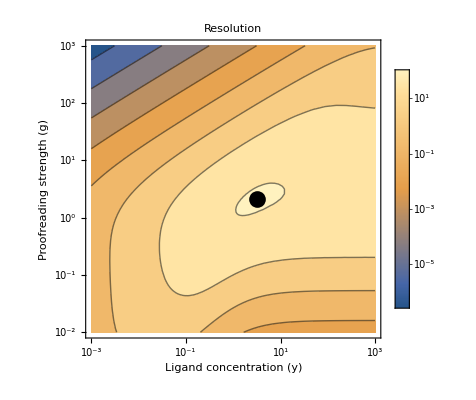

```mathematica
FigS1EFrameTicks={{Table[{i,Superscript[10,i]},{i,-2,3}],None},{Table[{i,Superscript[10,i]},{i,-3,3}],None}};
FigS1EtickSFs={1,0.573,0.59,0.67,0.43};
FigS1Eticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-7,2,2}];
FigS1Eticks=Table[{FigS1EtickSFs[[i]]*FigS1Eticks[[i,1]],FigS1Eticks[[i,2]]},{i,1,Length[FigS1Eticks]}];
FigS1EbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},LegendMarkerSize->240,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Eticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,1}},8,LegendMarkerSize->250,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1D=ContourPlot[Log10[KPR1BPk]/.xgParams,{ctest,-3,3},{gtest,-2,3},
Epilog->{PointSize[0.03],{Black,Point[{Log10[3.2],Log10[2.1]}]}},FrameLabel->{"Ligand concentration  (y)","Proofreading strength  (g)"},PlotLegends->FigS1EbarLegend,PlotLabel->"Resolution",LabelStyle->{Black,FontSize->18},TicksStyle->Black,FrameTicks->FigS1EFrameTicks,PlotRange->All]
```

#### S1E

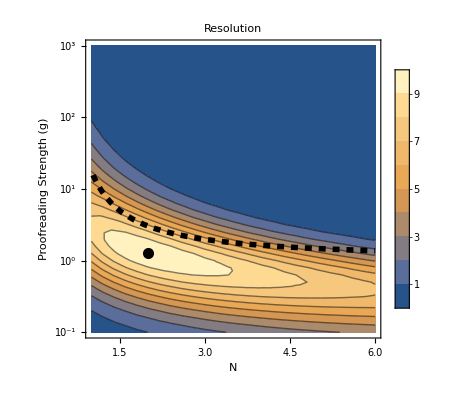

```mathematica
data=Flatten[Table[{NTEST,GTEST,BPMetric[koff,ΣkN]}/.xgParams/.{ctest->2,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.1},{NTEST,1,6,0.2}],1];
EpilogPoint=MaximalBy[data,Last][[1]];
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)"},
PlotLegends->Automatic,
PlotLabel->"Resolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}}};
FigS1E=Show[
ListContourPlot[data,Evaluate@plotOptions,
Epilog->{PointSize[0.02],{Black,Point[{EpilogPoint[[1]],EpilogPoint[[2]]}]}}],
Plot[(1-2^(1/Ns))/(-1+0.1 2^(1/Ns)),{Ns,1.03,6},PlotStyle->{Black,Dashed,Thickness[0.01]}]
]
```

#### S1F

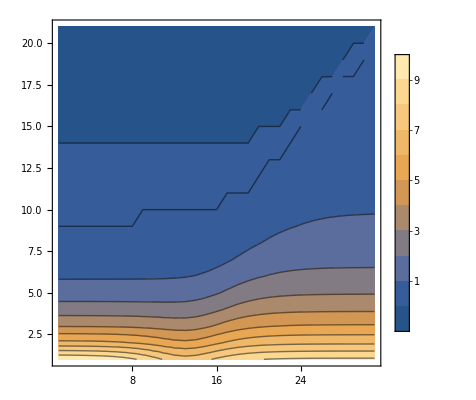

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,δ->0.1,c->10^ctest,kf->1};
FigS1F=ListContourPlot[Table[Ns/.NMaximize[{koff/√ΣkN/.estimateParams/.{ctest->CTEST,gtest->GTEST},Ns∈Reals&&Ns≥0},Ns][[2]],{GTEST,-1,3,0.2},{CTEST,-3,3,0.2}],PlotLegends->Automatic,PlotRange->All,Contours->Table[i,{i,0,10}]]
```

#### S1G

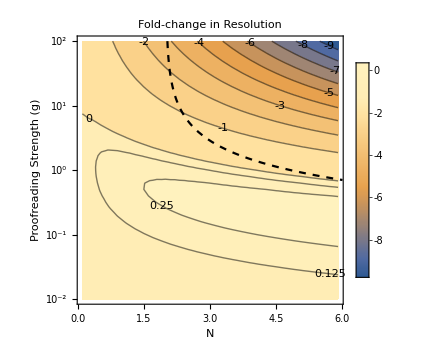

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->1,δ->0.5,c->10^ctest,kf->10^-gtest};
NMAX=6;
data=Flatten[Table[{NTEST,GTEST,Log10[BPMetric[koff,ΣkN]/BPMetric[koff,Σk0]]}/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-2,2,0.1},{NTEST,0.1,NMAX,0.2}],1];

plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)"},
PlotLegends->Automatic,
PlotLabel->"Fold-change in\nResolution",
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-2,3}],None},{Automatic,None}},
Contours->Evaluate@Join[Table[i,{i,1.75,0,-0.125}],Table[-i,{i,1,15}]],
ContourLabels->True,ImageSize->Medium,PlotRange->{-2 NMAX,1}};
FigS1G=ListContourPlot[data,Evaluate@plotOptions];

contour=Plot[Log10[(1-4^(1/Ntest))/(-1+0.5 4^(1/Ntest))],{Ntest,1,NMAX},PlotRange->{{0,NMAX},{-2,2}},PlotStyle->{Black,Dashed,Thickness->0.01},AspectRatio->1,ImageSize->Medium];
FigS1G=Show[FigS1G,contour]
```

#### S1H

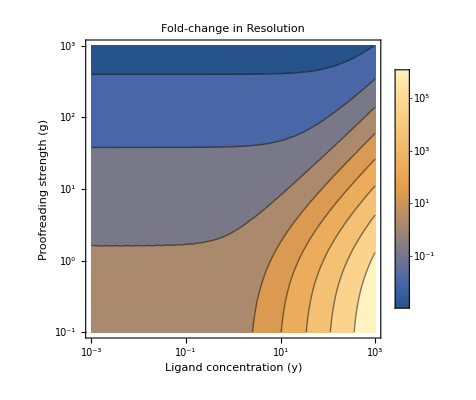

```mathematica
FigS1CtickSFs={1.6,0.55,0.89,0.97};
FigS1Cticks={#[[1]],Style[#[[2]],{Black,FontSize->18}]}&/@Table[{i,Superscript[10,i]},{i,-1,5,2}];
FigS1Cticks=Table[{FigS1CtickSFs[[i]]*FigS1Cticks[[i,1]],FigS1Cticks[[i,2]]},{i,1,Length[FigS1Cticks]}];
FigS1CbarLegend=Overlay[{BarLegend[{"M10DefaultDensityGradient",{-3.75,6}},LegendMarkerSize->200,LegendMargins->{{0,0},{20,0}},Ticks->FigS1Cticks,LabelStyle->Black],
BarLegend[{"M10DefaultDensityGradient",{-3.75,6}},8,LegendMarkerSize->200,LegendMargins->{{0,0},{20,0}},Ticks->None]}];

FigS1H=ContourPlot[Log10[KPR1BPk/KPR0BPk]/.xgParams,{ctest,-3,3},{gtest,-1,3},FrameLabel->{"Ligand concentration  (y)","Proofreading strength  (g)"},PlotLegends->FigS1CbarLegend,PlotLabel->"Fold-change in\nResolution",LabelStyle->{Black,FontSize->18},TicksStyle->Black,FrameTicks->xgTicks]
```

#### S2A

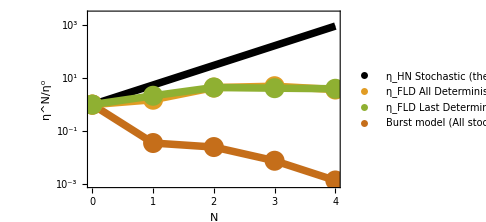

```mathematica
FigS2A=Legended[
Show[ListLogPlot[Table[{Ns,ηN/η0}/.xgParams/.testpoint,{Ns,0,4,1}],Frame->{{True,False},{True,False}},FrameLabel->{"N","η^N/η^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.001,2500}}],
p2,
ListLogPlot[AllDetFLD,PlotStyle->{cmap[[2]],PointSize[0.04]}],
ListLogPlot[AllDetFLD,Joined->True,PlotStyle->{cmap[[2]],Thickness[0.015]}],

(*ListLogPlot[AllDetHN,PlotStyle->{cmap[[4]],PointSize[0.04]}],
ListLogPlot[AllDetHN,Joined->True,PlotStyle->{cmap[[4]],Thickness[0.015]}],*)

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{cmap[[3]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{cmap[[3]],Thickness[0.015]}],


ListLogPlot[KPRGFLD1,PlotStyle->{cmap[[6]],PointSize[0.04]}],
ListLogPlot[KPRGFLD1,Joined->True,PlotStyle->{cmap[[6]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,(*cmap[[4]],*)cmap[[2]],cmap[[3]],cmap[[6]]},{"η_HN Stochastic (theory)",(*"η_HN Determinstic (sim)",*)"η_FLD All Deterministic","η_FLD Last Deterministic","Burst model (All stochastic)"},LegendMarkerSize->25]]
```

#### S2B

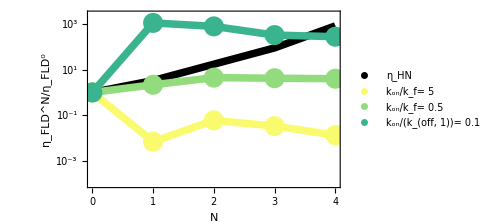

```mathematica
FigS2B=Legended[
Show[
ListLogPlot[HNReviwer2ModelSimMedC,Frame->{{True,False},{True,False}},FrameLabel->{"N","η_FLD^N/η_FLD^0"},PlotLegends->Automatic,LabelStyle->{Black,FontSize->18},TicksStyle->Black,Axes->False,PlotStyle->{PointSize[0.00],Black},FrameTicks->{{yticks,None},{{0,1,2,3,4},None}},PlotRange->{Automatic,{0.0001,2500}}],
(*LogPlot[KPRGNHN/KPRG0HN/.xgParams/.testpoint,{Ns,0,4},PlotStyle->{Thickness[0.015],Black}],*)

ListLogPlot[HNReviwer2ModelSimMedC,Joined->True,PlotStyle->{Black,Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFHighC,PlotStyle->{gradcolor[[1]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFHighC,Joined->True,PlotStyle->{gradcolor[[1]],Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,PlotStyle->{gradcolor[[3]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFF,Joined->True,PlotStyle->{gradcolor[[3]],Thickness[0.015]}],

ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFLowC,PlotStyle->{gradcolor[[5]],PointSize[0.04]}],
ListLogPlot[FLDReviewer2ModelSimτIs1OverKOFFLowC,Joined->True,PlotStyle->{gradcolor[[5]],Thickness[0.015]}],

ImageSize->Medium
],
PointLegend[{Black,gradcolor[[1]],gradcolor[[3]],gradcolor[[5]]},{"η_HN","k_on/k_f= 5","k_on/k_f= 0.5","k_on/(k_(off, 1))= 0.1"},LegendMarkerSize->25]]
```

#### S3

```mathematica
CF1=Log10[(μN/.koff->ζ koff)/μN+λ (μN/(√ΣN)/.koff->ζ koff)];
CF2=Log10[μN/(μN/.koff->ζ koff)+λ ((μN/(√ΣN))^-1/.koff->ζ koff)];
```

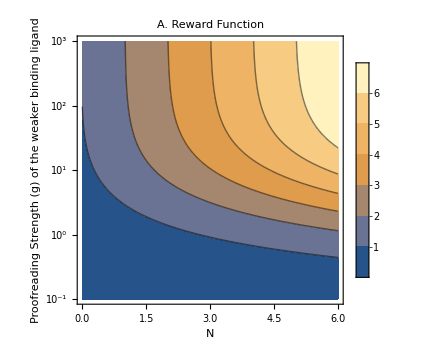
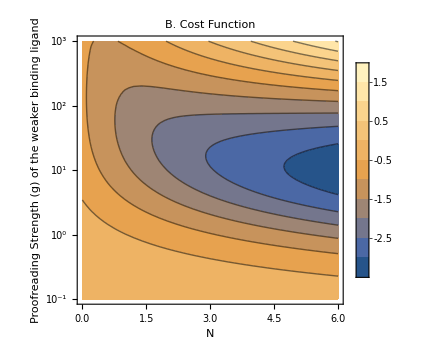

```mathematica
estimateParams={kon->1,kp->1,t->100,koff->10^gtest,c->10^ctest,kf->1,ζ->0.1,λ->10^-1};
plotOptions={
FrameLabel->{"N","Proofreading Strength  (g)\n of  the weaker binding ligand"},
PlotLegends->Automatic,
LabelStyle->{Black,FontSize->20},
TicksStyle->Black,
FrameTicks->{{Table[{i,Superscript[10,i]},{i,-1,3}],None},{Automatic,None}},
ImageSize->Medium};

data1=Flatten[Table[{NTEST,GTEST,CF1}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
S3A=ListContourPlot[data1,PlotLabel->"A. Reward Function",Evaluate@plotOptions];


data2=Flatten[Table[{NTEST,GTEST,CF2}/.expandParams/.estimateParams/.{ctest->0,gtest->GTEST,Ns->NTEST},{GTEST,-1,3,0.05},{NTEST,0,6,0.2}],1];
S3B=ListContourPlot[data2,PlotLabel->"B. Cost Function",Evaluate@plotOptions];
FigureS3=Row[{S3A,S3B}]
```

## Export Figures

```mathematica
savedir=FileNameJoin[{NotebookDirectory[],"Figures","Raw PDFs"}];
SetDirectory[savedir];
```

```mathematica
Export["Fig1B.pdf",Fig1B];
Export["Fig1C.pdf",Fig1C];
Export["Fig2A.pdf",Fig2A];
Export["Fig2B.pdf",Fig2B];
Export["Fig2C.pdf",Fig2C];
Export["Fig3A.pdf",Fig3A];
Export["Fig3B.pdf",Fig3B];
Export["Fig4A.pdf",Fig4A];
Export["Fig4B.pdf",Fig4B];
Export["Fig4C.pdf",Fig4C];

Export["FigS1A.pdf",FigS1A];
Export["FigS1B.pdf",FigS1B];
Export["FigS1C.pdf",FigS1C];
Export["FigS1D.pdf",FigS1D];
Export["FigS1E.pdf",FigS1E];
Export["FigS1F.pdf",FigS1F];
Export["FigS1G.pdf",FigS1G];
Export["FigS1H.pdf",FigS1H];

Export["FigS2A.pdf",FigS2A];
Export["FigS2B.pdf",FigS2B];

Export["FigS3.pdf",FigS3];
```